# Statistics Exam 2 Review

## Notes from practice Exams

## Normal Distributions

### Standardizing a normal

#### If I have a random variable x ~ N(μ,σ^2) and I need to get to a standard normal I know that (x-μ)/σ~N(0,1).

#### At this point I can use the standard normal chart to look up the zsocre that I get.

#### I will, at times need to solve for x. To do this I set (x-μ)/σ=z-score associated with the probablity the problem gave us. Plug μ and σ in and solve for x. It's that simple.

### Adding/Subtracting 2 Normals

#### I will be given two random variables each with their own μ and σ^2(say x and y).

#### If I am asked to find a value or probablitiy for the combined effect of the two I need to say x + y ~N (μ_x+ μ_y, σ_x^2+σ_y^2). I can then go through the normal process of standardization and use the table.

#### If I am asked to find that one is bigger or smaller than the other, that will be the difference. x - y ~ N(μ_x- μ_y, σ_x^2+σ_y^2+2Cov(x,y)) The reaso for the + in variance is because you factor out a (-1)^2 which makes them add. Usually they will be independent so the Cov part drops off. I find the z-score by this expression P(((x-y)-(μ_new))/(√(σ_new^2))≤ 0) That ends up simplifying to (x-y)≤μ_new/(√(σ_new^2)).

## Correlation Coefficient

### Corr (x, y) = (Cov(x, y))/(σ_x σ_y)

#### This requries a lot of computations. We need to find E(x), E(x), V(x), V(y), σ(x) ,σ(y) ,E(x^2),E(y^2),E(XY),Cov(x,y)

#### I sholud be able to do the expected value of x and y, but V(x)=E(x^2)-(E(x))^2, the same for y.

#### For the E(x^2) we just needed to do the same thing as E(x), but just square all the x terms.

#### σ is just √V.

#### Cov(x,y)=E(xy)-E(x)E(y)

## Cotinuous Distributions

### Continuous Conditional Density Functions

#### f_x(x|y)=(f(x,y))/(f_y(y))

### Esimating V and μ

#### How to find an estiamtor s^2

You will be given a list of data. Find the simple average of that and then s^2=(1/(n-1)(x_1-x^-)^2+...+(x_n-x^-)^2)

# Review Sheet from teacher

## Special Cotinuous Distributions

### Find mean, variance, pdf,cdf and percentiles for uniform, exponential, normal, and chi-square distributions.

E(x)= “mean” on table
V(x)= “Variace” on table
pdf(x)= “f(x)” on table
cdf(x)= “F(x)” on table
Percentile: if I am looking for the 95th percentile I say P(y≥ϕ_(.95))=.05 and look up the z-score associated with .05 on the chart.

### Find percentiles for t and F distributions

In this case you just need to do 1-percentile you are looking for as your α and then use the row corresponding to the df and give the z score.

### Know the approprite shape of the pdf for normal, uniform. Chi-Square, exponential, t, and F

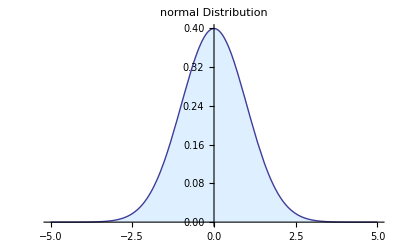
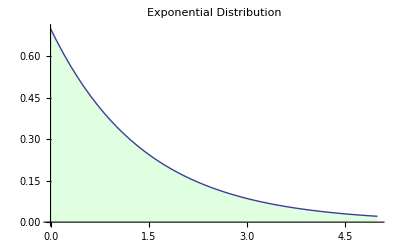
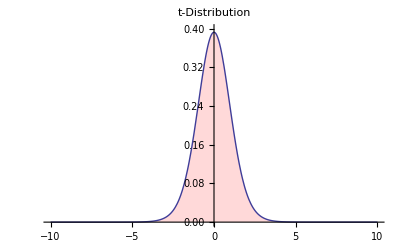
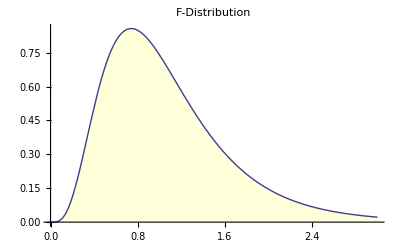
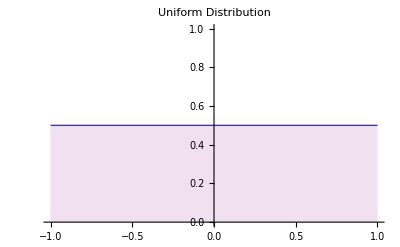
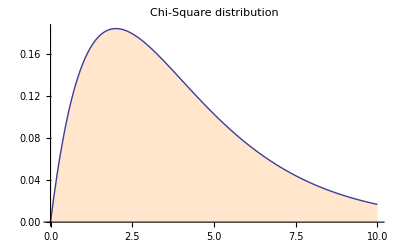

```mathematica
{Plot[PDF[NormalDistribution[0, 1], x], {x, -5, 5}, Filling -> Axis, PlotLabel -> "normal Distribution", FillingStyle -> LightBlue], Plot[PDF[ExponentialDistribution[.7], x], {x, 0, 5}, Filling -> Axis, PlotLabel -> "Exponential Distribution", FillingStyle -> LightGreen], Plot[PDF[StudentTDistribution[15], x], {x, -10, 10}, Filling -> Axis, FillingStyle -> LightRed, PlotLabel -> "t-Distribution", PlotRange -> {0, .4}], Plot[PDF[FRatioDistribution[10, 25], x], {x, 0, 3}, Filling -> Axis, PlotLabel -> "F-Distribution", FillingStyle -> LightYellow], Plot[PDF[UniformDistribution[{-1, 1}], x], {x, -1, 1}, Filling -> Axis, PlotLabel -> "Uniform Distribution", FillingStyle -> LightPurple], Plot[PDF[ChiSquareDistribution[4], x], {x, 0, 10}, Filling -> Axis, PlotLabel -> "Chi-Square distribution", FillingStyle -> LightOrange]}
```

## Joint Distributions

### Confirm that a joint Density function is valid

2 Cases:
1.) continuous distribution. If this is the case I need to integrate the pdf f(x,y) over the entire bounds for both x and y and assure that it eqauls 1. At times I will be asked to find a constant that makes the pdf a legit function and to do that I simply need to do the integral, set it equal to zero, and solve for the constant.
2) it is a discrete Distribution: I need to confirm that they sum of all probabliilties is 1. Same case for constants as the continuous section above, except that I won’t need to integrate.

### Find Joint Probabilities (such as P(X>1,Y<3) or P(X>Y))

2 cases:
1.) Continuous distributions: In exapmle one I would do this ∫_1^upper (∫_lower^3 f(x,y)ⅆy)ⅆx and in example 2 I would do this ∫_y^upper (∫_0^x f(x,y)ⅆy)ⅆx
2.) Discrete Distrbiution: I would need to find the conditional dsitributions taht satisfy the bounds placed on me in the discription of the problem.

### Find Marginal Densities form the joint density

2 cases:
1.) continuous: I would find f_x by integrating f(x,y)∂y from y's lower bound to y's upper bound. This could be tricky if the values for x and y depend on eachother or and interrelated. 
2.) Discrete. I would simply need to make the table for probabilities associated with a combination of x and y. From there I would simply sum the rows adn columns to get the marginal distributions for whichever variable is represented on by  rows and columns.

### Determine whether X and Y are independent

2 Cases, but same process. The definintion of independent is if the product of the marginal densities is equal to the joint density. so f_x f_y=f(x,y)

### Find the Expected value of a random function of random variables (such as E(X^2 Y)

Two cases:
1.) Continuous distributions: I would go through the same process I would for any expected value, but this time I would multiply the joint density function by whatever function of the variables I want to know the expected value for (in this case (x^2 y). ∫_lower^upper (∫_lower^upper x^2 y*f(x,y)ⅆy)ⅆx
2.) Discrete Distributions: I would take the individual probabilites that x is some value and y is another and multiplly that probablitiy by (associated x value^2)(Associated y value).

### Find the Covariance(x,y)=σ_xy

The equation is Cov(x,y)=E(xy)-E(x)E(y)
1.) Continuous distribution: To find E(xy) solve this integral ∫_lower^upper (∫_lower^upper x*y*f(x,y)ⅆx)ⅆy. To find E(x) or E(y) solve this integral, ∫_lower^upper x*f_x(x)ⅆx

### Algebra Tricks

Cov(3x,-4y)=3*-4*Cov(x,y)
Cov(x,number)=0
Cov(x+y,z)=Cov(x,z)+Cov(y,z)
Var(2x)=2^2 Var(x)
Var(-x)=(-1)^2 Var(x)=Var(x)
Var(3x,-2y)=V(3x)+V(2y)+2Cov(3x,-2y)=9V(x)+4V(y)-12Cov(x,y)

### Finding the Correlation Coefficient

Corr (x, y) = (Cov(x, y))/(σ_x σ_y), We have already talked about finding Cov(x,y) and V(x),V(y) so just remember the equation.

### Understand the relationship between correlation and independence

If the Corr(x,y)=0 that doesn’t mean that they are independent. However, if they are independent the Corr(x,y)=0.

### Understand the Relationship between correlation and causation

Correlation doesn’t imply causation. So if two things have a strong correlation it doesn’t nessicarily mean that one causes the other

## Estimation and Inference

### Understand what is meand by i.i.d.

This means Independently and Identically distributed. That means that the data was collected in such a way that all the data has the same distribution (indentically) and that collecting from one portion in the sample didn’t effect the other sections (independent)

### Understand what is mean by an esimator and its distribution

An estimator is a function that produces and estimate for example 1/n∑_(i=1)^n x_iIs an estimator for the mean of a function. It produces the estimate x^-.
To be honest I am not really sure what the distribution part is all about

### Understand the means and significance and meaning of the central limit theorem

The central Limit theorem says that no matter what distribution the data initially had, as you increase the sample size enough, that distribution begins to look like a normal distribution. (as a rule of thumb we say that 30 is a large sample size).
This is very important because it helps us be able to extimate functions and distributions of data taht otherwise don’t have distributions or have distributions that are very difficult to work with.

### Be able to compute common statistics x^-,s^2,s,p̂

to compute x^-we usually just say x^-=1/n∑_(i=1)^n x_i
s^2=1/(n-1)∑_(i=1)^n (x-x^-)^2
s=√(s^2)
p̂=(# of succeses)/(# of trials), that is usually how we do it at least.

### Derive the mean and variance of simple estimators

Just remember that the E(s^2)=σ^2 and the E(x^-)=μ

### Determine wheteher and estimator is unbiased, efficient, and/or consistent

Bias(θ̂)=E(θ̂-θ)=E(θ̂)-E(θ)
Efficiency says lim(V(θ̂),n→ ∞)=0 (NOTE when comparing two estimators, if the variance of one is lower than the variance of the other than the lower one is more efficient)
Consistency says that the estimator is effecient and that lim(E(θ̂),n→ ∞)=0

### Use the Method of Moments to obtain parameter extimates for given distributions

The method of moments tells us that we can solve for say E(x) in the normal way, but with symbols instead of values, and then set that eqaul to x^-and solve for x^-.
To do it for s^2we would solve for variance in the normal way and then set is equal to s^2 and solve for s^2.

### Use the metohd of maximum liklihood to obtain parameter estimates for given distributions

In this case we will either be given a pdf or told what kind of distribution we are dealing with so we can look the pdf up.
then the steps are as follows:
L=∏_(i=1)^n pdf
l=ln(L)
l=∑_(i=1)^n ln(pdf)
Simplify l 
set (∂l)/(∂paramter)=0 and solve for the parameter. (If I am trying to find σ^2 I need to take the deriviatve with respect to σ, not σ^2)

### Find the margin of error associated with a point estimate

First we should know that a point estimate is either the simple average (x^-) or simple probablitiy (p̂)
To find the margin of error associated with x^- we do √((σ^2)/n)and if we don't know σ^2 we use s^2, n is the number of samples or trials.
To find the margin of error associated with p̂ we do √((p̂*(1-p̂))/n)(if we know or are testing a value for p, use that in place of p̂, n is the number of observations.)

### Derive a one-sided or two-sided confidence interval for μ_1,μ_1-μ_2,p, or p_1-p_2.

A one sided confidence interval says we take one of the following:
μ=x^-±√(σ^2/n) the + or  - comes from what the question asks for
μ_1-μ_2=((x^-)_1-(x^-)_2)±√(σ_1^2/n_1+σ_2^2/n_2), again use s^2 if σ^2 is unknown.
p = p̂±√((OverHat[(p](1-p̂)))/n)

p_1-p_2=((p̂)_1-(p̂)_2)±√(((p̂)_1*(1-(p̂)_1))/n_1+((p̂)_2*(1-(p̂)_2))/n_2)

A two sided test is the same thing, excpect we do both sides of the ± instead of just one of them.

### Estimate Probabilities associated with μ_1,μ_1-μ_2,p, or p_1-p_2 such as P(μ>500)

To do this example we would say (x^--μ)/(√(σ^2/n))= some z-score they give us and we look it up on either the t or normal charts. (see below under section when to use normal and when to use t)
We would plug in the estimated mean for x^- and the real mean we are testing (in this case 500) for μ and obviously we know what σ^2and n are.

### Formulate null along with one/two-sided aldernitice hypotheses for μ_1,μ_1-μ_2,p, or p_1-p_2 and test the null hypothesis at any α level . Calculate the test statistic, critical value ofr rejection region, and p-value

I can’t really write down how to do this, but essentially a one sided alternative hypothesis contains an inequality and a two sided contains the ≠ sign. 
The critical value is the z-score associated with the α they gave us
the p-value is the probabliity of our test statistic
the test statistic is the z-score value obtained from using one of the equations laid out above under the derive a confidence interval part.

### When to use normal or t charts

(x^--μ)/(√(s^2/n))~ t(n-1). This means that if n is ≤30 then we would use a t-chart with n-1 df. 
If n ≤30 the t looks so much like a normal that we just use that chart. If we are told the distribution is normal, we use the normal chart.

### Relationships between contiuous distributions

If w ~ x^2(u) and z ~ x^2(o) then (w/υ)/(z/0)~F(υ,o)
If A ~ N(0,1) and B ~ x^2(υ), then A/(√B)~t(υ)